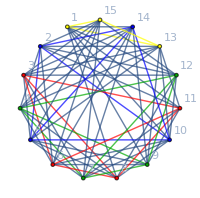
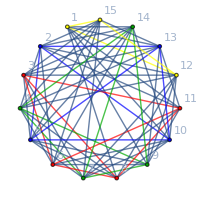
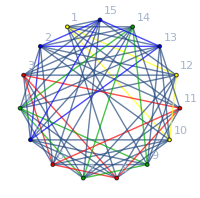
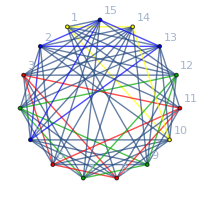
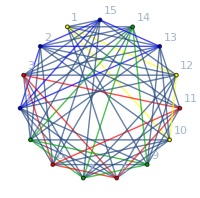
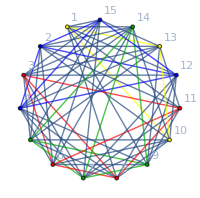
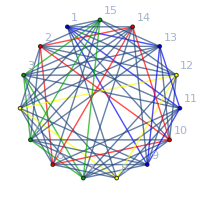
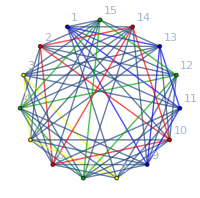

```mathematica
With[{g=Graph[plantri[[3]]]},
With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
Table[
With[{sets=SymbolToSets[formula], colors={Blue,Red,Darker[Green],Yellow}},
Graph[GraphComplement[g],
VertexStyle->Flatten[
Table[Map[#-> colors[[k]]&,sets[[k]] ],{k,Length[sets]}]
],
EdgeStyle->Flatten[
Table[Map[#[[1]]<->#[[2]]-> {Thick,colors[[k]]}&,Subsets[sets[[k]],{2}] ],{k,Length[sets]}]
],
ImageSize->200,
VertexLabels->"Name"
]
],
{formula,Select[form,Length[SymbolToSets[#]]==4&]}
]]
]
```

```mathematica
IntegerPartitions[66,{4}]
```

{{63,1,1,1},{62,2,1,1},{61,3,1,1},{61,2,2,1},{60,4,1,1},{60,3,2,1},{60,2,2,2},{59,5,1,1},{59,4,2,1},{59,3,3,1},{59,3,2,2},{58,6,1,1},{58,5,2,1},{58,4,3,1},{58,4,2,2},{58,3,3,2},{57,7,1,1},{57,6,2,1},{57,5,3,1},{57,5,2,2},{57,4,4,1},{57,4,3,2},{57,3,3,3},{56,8,1,1},{56,7,2,1},{56,6,3,1},{56,6,2,2},{56,5,4,1},{56,5,3,2},2029,{20,18,14,14},{20,17,17,12},{20,17,16,13},{20,17,15,14},{20,16,16,14},{20,16,15,15},{19,19,19,9},{19,19,18,10},{19,19,17,11},{19,19,16,12},{19,19,15,13},{19,19,14,14},{19,18,18,11},{19,18,17,12},{19,18,16,13},{19,18,15,14},{19,17,17,13},{19,17,16,14},{19,17,15,15},{19,16,16,15},{18,18,18,12},{18,18,17,13},{18,18,16,14},{18,18,15,15},{18,17,17,14},{18,17,16,15},{18,16,16,16},{17,17,17,15},{17,17,16,16}}
 |  |  |  |

```mathematica
Select[IntegerPartitions[14,{4}],MemberQ[Range[5],#[[1]]]&&MemberQ[Range[5],#[[2]]]&&MemberQ[Range[5],#[[3]]]&]
```

{{5,5,3,1},{5,5,2,2},{5,4,4,1},{5,4,3,2},{5,3,3,3},{4,4,4,2},{4,4,3,3}}

```mathematica
EdgeCount[GraphComplement[plantri[[2]]]]
```

55

```mathematica
EdgeCount[GraphComplement[plantri[[1]]]]-(4*3)
```

24

```mathematica
VertexCount[GraphComplement[plantri[[2]]]]
```

14

```mathematica
EdgeCount[GraphComplement[plantri[[2]]]]-(2*6+2*3)
```

37

```mathematica
EdgeCount[GraphComplement[plantri[[3]]]]-(6*3+3)
```

45

```mathematica
PartitionsP
```

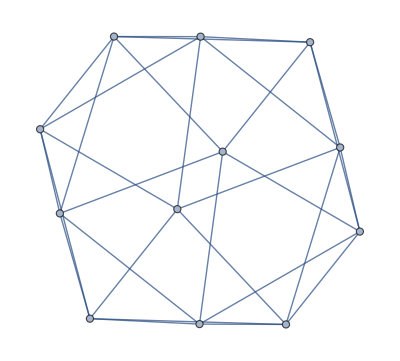
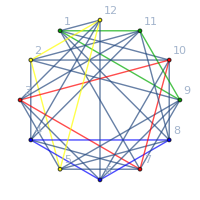
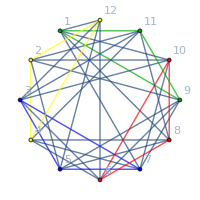
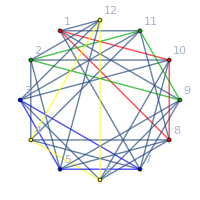
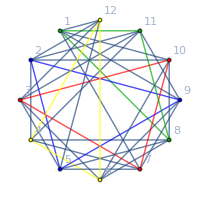
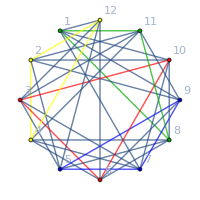
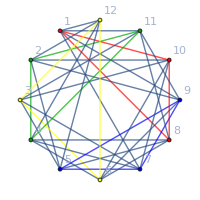
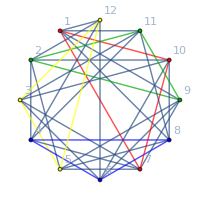
-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{g=Graph[plantri[[1]]]},
With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
g->
Table[
With[{sets=SymbolToSets[formula], colors={Blue,Red,Darker[Green],Yellow}},
Graph[GraphComplement[g],
VertexStyle->Flatten[
Table[Map[#-> colors[[k]]&,sets[[k]] ],{k,Length[sets]}]
],
EdgeStyle->Flatten[
Table[Map[#[[1]]<->#[[2]]-> {Thick,colors[[k]]}&,Subsets[sets[[k]],{2}] ],{k,Length[sets]}]
],
ImageSize->200,
VertexLabels->"Name"
]
],
{formula,Select[form,Length[SymbolToSets[#]]==4&]}
]]
]
```

```mathematica
JacobsThalGraph[2]
```

True

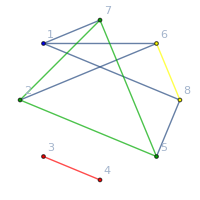
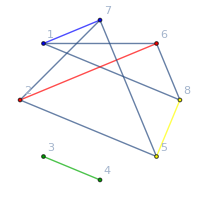
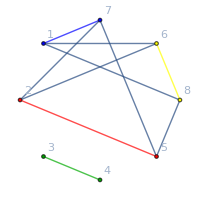
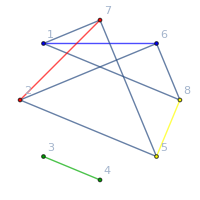
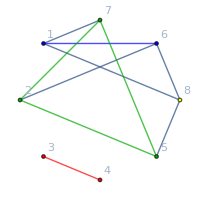
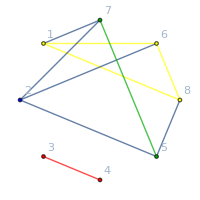
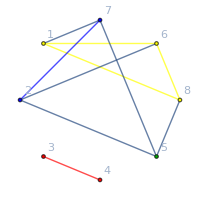
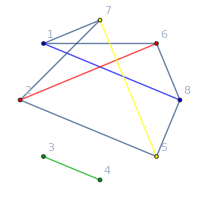

```mathematica
With[{g=JacobsThalGraph[4]},
With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
Table[
With[{sets=SymbolToSets[formula], colors={Blue,Red,Darker[Green],Yellow}},
Graph[GraphComplement[g],
VertexStyle->Flatten[
Table[Map[#-> colors[[k]]&,sets[[k]] ],{k,Length[sets]}]
],
EdgeStyle->Flatten[
Table[Map[#[[1]]<->#[[2]]-> {Thick,colors[[k]]}&,Subsets[sets[[k]],{2}] ],{k,Length[sets]}]
],
ImageSize->200,
VertexLabels->"Name"
]
],
{formula,Select[form,Length[SymbolToSets[#]]==4&]}
]]
]
```

```mathematica
Table[
With[{g=JacobsThalGraph[m]},
g->With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
Table[
With[{sets=SymbolToSets[formula], colors={Blue,Red,Darker[Green],Yellow}},
Graph[GraphComplement[g],
VertexStyle->Flatten[
Table[Map[#-> colors[[k]]&,sets[[k]] ],{k,Length[sets]}]
],
EdgeStyle->Flatten[
Table[Map[#[[1]]<->#[[2]]-> {Thick,colors[[k]]}&,Subsets[sets[[k]],{2}] ],{k,Length[sets]}]
],
ImageSize->200,
VertexLabels->"Name"
]
],
{formula,Select[form,Length[SymbolToSets[#]]==3&]}
]]
],{m,1,9}]
```

$Aborted

```mathematica
MatrixForm[
Table[
With[{g=JacobsThalGraph[m]},
With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
Table[
Total[
Table[
1,
{formula,Select[form,Length[SymbolToSets[#]]==p&]}
]],
{p,3,11}
]]
],{m,1,8}]]
```

(0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 3 | 3 | 1 | 0 | 0 | 0 | 0 | 0
0 | 5 | 10 | 6 | 1 | 0 | 0 | 0 | 0
1 | 11 | 30 | 29 | 10 | 1 | 0 | 0 | 0
0 | 21 | 91 | 126 | 70 | 15 | 1 | 0 | 0
1 | 43 | 273 | 525 | 420 | 146 | 21 | 1 | 0
0 | 85 | 820 | 2142 | 2331 | 1170 | 273 | 28 | 1
1 | 171 | 2460 | 8653 | 12390 | 8427 | 2835 | 470 | 36)

```mathematica
Total[{1,11 ,30 ,29 ,10, 1}]
```

82

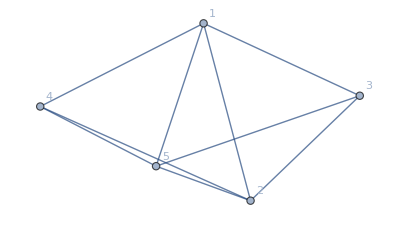
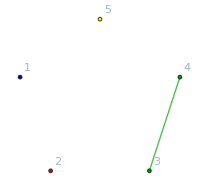
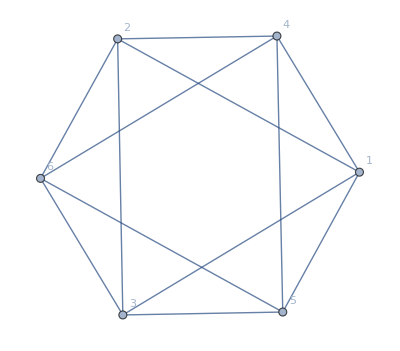
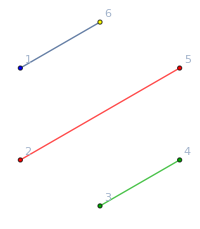
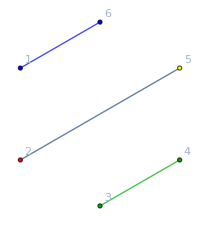
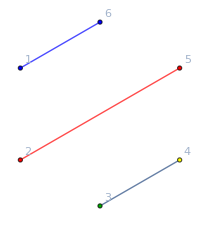
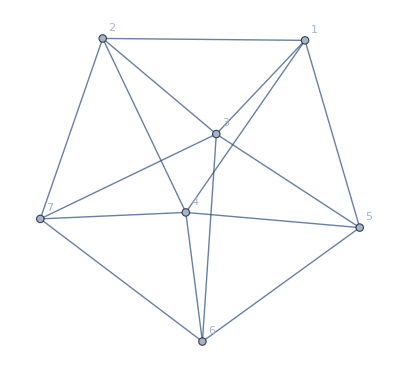
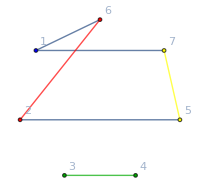
{-Graphics-→{-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[
With[{g=JacobsThalGraph[m]},
Graph[g,VertexLabels->"Name"]->With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
Table[
With[{sets=SymbolToSets[formula], colors={Blue,Red,Darker[Green],Yellow}},
Graph[GraphComplement[g],
VertexStyle->Flatten[
Table[Map[#-> colors[[k]]&,sets[[k]] ],{k,Length[sets]}]
],
EdgeStyle->Flatten[
Table[Map[#[[1]]<->#[[2]]-> {Thick,colors[[k]]}&,Subsets[sets[[k]],{2}] ],{k,Length[sets]}]
],
ImageSize->200,
VertexLabels->"Name"
]
],
{formula,Select[form,Length[SymbolToSets[#]]==4&]}
]]
],{m,1,7}]
```